```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

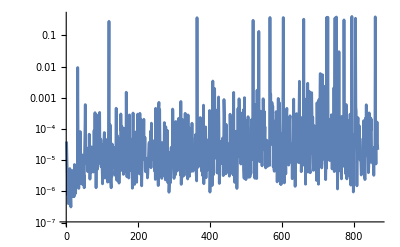

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-20.2687,L2PhaseSet→-38.4287,Q1EkG→126.633,Q2EkG→-150.429,Q3EkG→110.331,Q4EkG→163.337,Q5EkG→-22.2834,Q6EkG→-152.15,S1ELkG→1248.45,S2ELkG→-3552.82,S3ELkG→-2440.83,S3ERkG→-567.602,S2ERkG→-3597.93,S1ERkG→1313.1,PDrive_mean_x→0.0000263066,PDrive_mean_y→6.766×10^-7,PDrive_sigma_x→0.000402661,PDrive_sigma_y→0.0000180364,PDrive_xCost→0.000403519,PDrive_yCost→0.0000180491,PDrive_totalCost→0.000210784,PDrive_emitSI90_x→0.000161582,PDrive_emitSI90_y→0.0000257982,PDrive_zLen→0.0000498707,PDrive_zCentroid→991.332,PWitness_mean_x→0.0000225478,PWitness_mean_y→-1.1346×10^-6,PWitness_sigma_x→0.000234953,PWitness_sigma_y→0.0000241712,PWitness_xCost→0.000236033,PWitness_yCost→0.0000241978,PWitness_totalCost→0.000130115,PWitness_emitSI90_x→0.0000488834,PWitness_emitSI90_y→5.2872×10^-6,PWitness_zLen→9.2928×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000208836,transverseCentroidOffset→4.1724×10^-6,maximizeMe→0.400743|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -20.2686798306
L2PhaseSet : -38.4286675314
Q1EkG : 126.6331212906
Q2EkG : -150.4291119206
Q3EkG : 110.3306802921
Q4EkG : 163.3368357055
Q5EkG : -22.2833970948
Q6EkG : -152.1496033604
S1ELkG : 1248.4517307997
S2ELkG : -3552.8158888263
S3ELkG : -2440.8280657528
S3ERkG : -567.6024425206
S2ERkG : -3597.9310230802
S1ERkG : 1313.1011317056
PDrive_mean_x : 0.0000263066
PDrive_mean_y : 6.766e-7
PDrive_sigma_x : 0.0004026606
PDrive_sigma_y : 0.0000180364
PDrive_xCost : 0.0004035191
PDrive_yCost : 0.0000180491
PDrive_totalCost : 0.0002107841
PDrive_emitSI90_x : 0.000161582
PDrive_emitSI90_y : 0.0000257982
PDrive_zLen : 0.0000498707
PDrive_zCentroid : 991.3317175312
PWitness_mean_x : 0.0000225478
PWitness_mean_y : -1.1346e-6
PWitness_sigma_x : 0.0002349533
PWitness_sigma_y : 0.0000241712
PWitness_xCost : 0.0002360328
PWitness_yCost : 0.0000241978
PWitness_totalCost : 0.0001301153
PWitness_emitSI90_x : 0.0000488834
PWitness_emitSI90_y : 5.2872e-6
PWitness_zLen : 9.2928e-6
PWitness_zCentroid : 991.3319263676
bunchSpacing : 0.0002088364
transverseCentroidOffset : 4.1724e-6
maximizeMe : 0.4007434582

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

4.17241×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv